{Binding Energy cs, bs, cc, bc, bb}

-0.0246512

-0.0319728

-0.0771792

-0.100745

-0.128011

{Ωcc 1/2+}

{3.72631,4.49142,{3.07333,2.93896,2.45719,2.04279}}

{0.476258}

{{0.326423},{0.309185}}

{Ωcc^* 3/2+}

{3.81983,4.68746,{3.07616,2.94672,2.46928,2.04279}}

{0.495399}

{{0.124097},{0.117544}}

{Ωbb 1/2+}

{10.4077,3.83046,{3.06173,2.90783,2.41367,2.04279}}

{0.450249}

{{0.0277821},{0.0263149}}

{Ωbb^* 3/2+}

{10.4507,3.9655,{3.06441,2.91491,2.42292,2.04279}}

{0.465418}

{{-0.282541},{-0.26762}}

{Ωccc 3/2+}

{4.84092,4.22122,{3.06902,2.92725,2.43993,2.04279}}

{0.680667}

{{0.548596},{0.519625}}

{Ωccb 1/2+}

{8.1132,3.74529,{3.05994,2.90314,2.40773,2.04279}}

{0.439797}

{{0.24899},{0.235841}}

{Ωccb^* 3/2+}

{8.13457,3.83219,{3.06177,2.90792,2.41379,2.04279}}

{0.448967}

{{0.326882},{0.30962}}

{Ωcbb 1/2+}

{11.3745,3.18261,{3.04581,2.86708,2.36645,2.04279}}

{0.111759}

{{-0.0999887},{-0.0947083}}

{Ωcbb^* 3/2+}

{11.4035,3.31336,{3.04951,2.87634,2.37637,2.04279}}

{0.114241}

{{0.109691^□},{0.103898}}

{Ωbbb 3/2+}

{14.6257,2.5876,{3.02445,2.81601,2.31856,2.04279}}

{0.283505}

{{-0.0949397},{-0.089926}}

{Mass Spectrum}

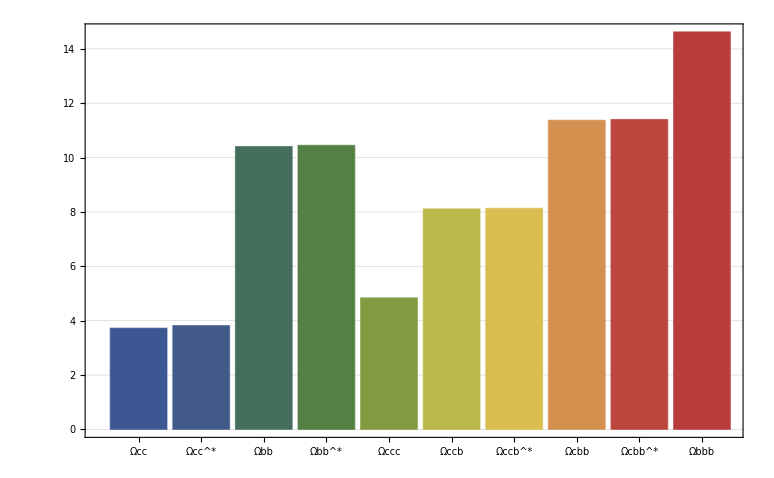

{Charge Radius}

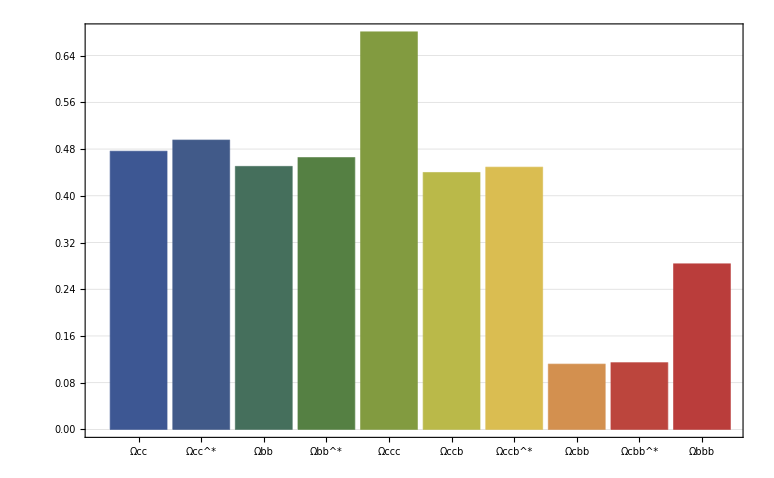

{Magnetic Moment}

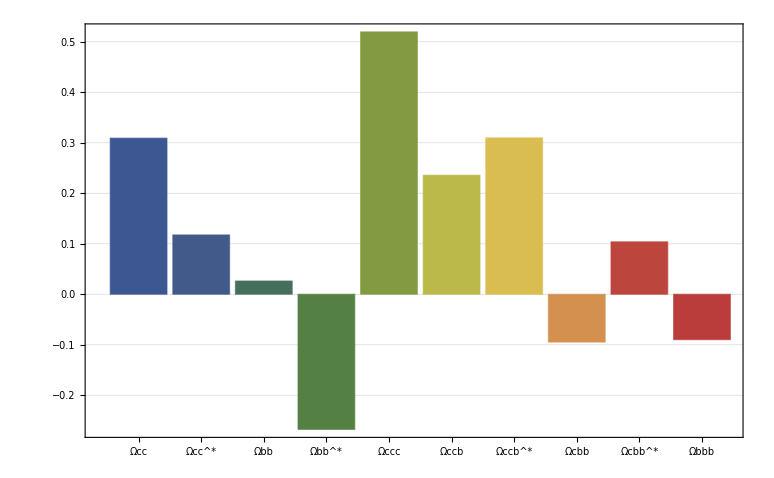

```mathematica
<<MITBagModel\MITBagModel.m

Nc=Hadron[{0,0,0,3},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,8}},0];
μNp=MagneticMoment[{0,0,0,4/3,-1/3},{0,0,0,0,0},Nc];

{"Binding Energy cs, bs, cc, bc, bb"}
Bcs=-(First[Hadron[{0,1,1,0},{{0,0,0,0},{0,0,-16/3,0},{0,0,0,0},{0,0,0,0}},0]]-2.112)/2
Bbs=-(First[Hadron[{1,0,1,0},{{0,0,-16/3,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},0]]-5.415)/2
Bcc=-(First[Hadron[{0,2,0,0},{{0,0,0,0},{0,-16/3,0,0},{0,0,0,0},{0,0,0,0}},0]]-3.097)/2
Bbc=-(First[Hadron[{1,1,0,0},{{0,16,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},0]]-6.275)/2
Bbb=-(First[Hadron[{2,0,0,0},{{-16/3,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},0]]-9.460)/2

{"Ωcc 1/2+"}
Ωcc=Hadron[{0,2,1,0},{{0,0,0,0},{0,-8/3,32/3,0},{0,0,0,0},{0,0,0,0}},2Bcs+Bcc]
rΩcc=ChargeRadius[{0,2,1,0,0},{0,0,0,0,0},Ωcc];
μΩcc=MagneticMoment[{0,4/3,-1/3,0,0},{0,0,0,0,0},Ωcc];
{rΩcc}
{{μΩcc},{μΩcc/μNp}}

{"Ωcc^* 3/2+"}
ΩccStar=Hadron[{0,2,1,0},{{0,0,0,0},{0,-8/3,-16/3,0},{0,0,0,0},{0,0,0,0}},2Bcs+Bcc]
rΩccStar=ChargeRadius[{0,2,1,0,0},{0,0,0,0,0},ΩccStar];
μΩccStar=MagneticMoment[{0,2,1,0,0},{0,0,0,0,0},ΩccStar];
{rΩccStar}
{{μΩccStar},{μΩccStar/μNp}}

{"Ωbb 1/2+"}
Ωbb=Hadron[{2,0,1,0},{{-8/3,0,32/3,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},2Bbs+Bbb]
rΩbb=ChargeRadius[{2,0,1,0,0},{0,0,0,0,0},Ωbb];
μΩbb=MagneticMoment[{4/3,0,-1/3,0,0},{0,0,0,0,0},Ωbb];
{rΩbb}
{{μΩbb},{μΩbb/μNp}}

{"Ωbb^* 3/2+"}
ΩbbStar=Hadron[{2,0,1,0},{{-8/3,0,-16/3,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},2Bbs+Bbb]
rΩbbStar=ChargeRadius[{2,0,1,0,0},{0,0,0,0,0},ΩbbStar];
μΩbbStar=MagneticMoment[{2,0,1,0,0},{0,0,0,0,0},ΩbbStar];
{rΩbbStar}
{{μΩbbStar},{μΩbbStar/μNp}}

{"Ωccc 3/2+"}
Ωccc=Hadron[{0,3,0,0},{{0,0,0,0},{0,-8,0,0},{0,0,0,0},{0,0,0,0}},3Bcc]
rΩccc=ChargeRadius[{0,3,0,0,0},{0,0,0,0,0},Ωccc];
μΩccc=MagneticMoment[{0,3,0,0,0},{0,0,0,0,0},Ωccc];
{rΩccc}
{{μΩccc},{μΩccc/μNp}}

{"Ωccb 1/2+"}
Ωccb=Hadron[{1,2,0,0},{{0,32/3,0,0},{0,-8/3,0,0},{0,0,0,0},{0,0,0,0}},2Bbc+Bcc]
rΩccb=ChargeRadius[{1,2,0,0,0},{0,0,0,0,0},Ωccb];
μΩccb=MagneticMoment[{-1/3,4/3,0,0,0},{0,0,0,0,0},Ωccb];
{rΩccb}
{{μΩccb},{μΩccb/μNp}}

{"Ωccb^* 3/2+"}
ΩccbStar=Hadron[{1,2,0,0},{{0,-16/3,0,0},{0,-8/3,0,0},{0,0,0,0},{0,0,0,0}},2Bbc+Bcc]
rΩccbStar=ChargeRadius[{1,2,0,0,0},{0,0,0,0,0},ΩccbStar];
μΩccbStar=MagneticMoment[{1,2,0,0,0},{0,0,0,0,0},ΩccbStar];
{rΩccbStar}
{{μΩccbStar},{μΩccbStar/μNp}}

{"Ωcbb 1/2+"}
Ωcbb=Hadron[{2,1,0,0},{{-8/3,32/3,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},2Bbc+Bbb]
rΩcbb=ChargeRadius[{2,1,0,0,0},{0,0,0,0,0},Ωcbb];
μΩcbb=MagneticMoment[{4/3,-1/3,0,0,0},{0,0,0,0,0},Ωcbb];
{rΩcbb}
{{μΩcbb},{μΩcbb/μNp}}

{"Ωcbb^* 3/2+"}
ΩcbbStar=Hadron[{2,1,0,0},{{-8/3,-16/3,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},2Bbc+Bbb]
rΩcbbStar=ChargeRadius[{2,1,0,0,0},{0,0,0,0,0},ΩcbbStar];
μΩcbbStar=MagneticMoment[{2,1,0,0,0},{0,0,0,0,0},ΩcbbStar];
{rΩcbbStar}
{{μΩcbbStar^□},{μΩcbbStar/μNp}}

{"Ωbbb 3/2+"}
Ωbbb=Hadron[{3,0,0,0},{{-8,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},3Bbb]
rΩbbb=ChargeRadius[{3,0,0,0,0},{0,0,0,0,0},Ωbbb];
μΩbbb=MagneticMoment[{3,0,0,0,0},{0,0,0,0,0},Ωbbb];
{rΩbbb}
{{μΩbbb},{μΩbbb/μNp}}

{"Mass Spectrum"}
BarChart[{First[Ωcc],First[ΩccStar],First[Ωbb],First[ΩbbStar],First[Ωccc],First[Ωccb],First[ΩccbStar],First[Ωcbb],First[ΩcbbStar],First[Ωbbb]},Frame->True,ChartLabels->{"Ωcc","Ωcc^*","Ωbb","Ωbb^*","Ωccc","Ωccb","Ωccb^*","Ωcbb","Ωcbb^*","Ωbbb"},ChartStyle->"DarkRainbow",GridLines->Automatic,GridLinesStyle->Directive[Gray, Dashed]]

{"Charge Radius"}
BarChart[{rΩcc,rΩccStar,rΩbb,rΩbbStar,rΩccc,rΩccb,rΩccbStar,rΩcbb,rΩcbbStar,rΩbbb},Frame->True,ChartLabels->{"Ωcc","Ωcc^*","Ωbb","Ωbb^*","Ωccc","Ωccb","Ωccb^*","Ωcbb","Ωcbb^*","Ωbbb"},ChartStyle->"DarkRainbow",GridLines->Automatic,GridLinesStyle->Directive[Gray, Dashed]]

{"Magnetic Moment"}
BarChart[{μΩcc/μNp,μΩccStar/μNp,μΩbb/μNp,μΩbbStar/μNp,μΩccc/μNp,μΩccb/μNp,μΩccbStar/μNp,μΩcbb/μNp,μΩcbbStar/μNp,μΩbbb/μNp},Frame->True,ChartLabels->{"Ωcc","Ωcc^*","Ωbb","Ωbb^*","Ωccc","Ωccb","Ωccb^*","Ωcbb","Ωcbb^*","Ωbbb"},ChartStyle->"DarkRainbow",GridLines->Automatic,GridLinesStyle->Directive[Gray, Dashed]]
```